# Lab 2 – Enzyme kinetics

Week 2: This week we will start to work with ODEs and how to use them to solve enzyme kinetics that use the law of mass action. Also we will look at some data and analyze it.

## Background

Law of mass action

Biochemical kinetics is based on the mass action law, introduced by Guldberg and Wagge in the 19th century. It states that the reaction rate is proportional to the probability of a collision of the reactants. This probability is in turn proportional to the concentration of reactants to the power of the molecularity, i.e., the number in which they enter the specific reaction. For a simple reaction of molecules A and B with k_+ and k_- the so-called kinetic or rate constants:
 
      A  +  B (⇌_(k_-))^(k_+)  2 P

the net reaction rate equals the forward rate minus the backward rate. The forward rate is a function of the concentrations of A and B times the forward kinetic rate constant k_+. The backward rate is a function of concentration P times the backward kinetic rate constant k_-:

v = v_++v_-= k_+A B-k_-P^2
where v is the net rate , v_+ the rate of the forward reaction and v_- the rate of the backward reaction. The dynamics (of the concentration) for this sytem is descibed by the following ODEs 
 
dA/dt=dB/dt=- v  ,    dP/dt=2 v.
 
 The genral mass action law for a reaction with substrate S_i and product concentration P_j reads:
 
   v = v_+-v_- = k_+ ∏_i S_i^m_i - k_-∏_j P_j^m_j,
   
where m_i and m_j denote the respective molecularities of S_i and P_jin this reaction.
The rate constants are related to the equlibrium constant in the following way :

K_eq = (k_+)/(k_-) =(∏_j P_j^m_j)/(∏_i S_i^m_i)

Basic enzyme kinetics – Michaelis-Menten equation

Consider a simple enzyme catalyzed reaction where the reaction of substrate S to form a product P is catalyzed by an enzyme E. ES is the enzyme-substrate complex in which enzyme and substrate are bound together :
     E + S (⇌_(k_-1))^(k_(+1)) ES →^(k_(+2)) E + P
With the condition that the reaction is in a steady state (i.e. ES is being made at the same rate as it is being broken down) and a couple of additional assumptions, if we denote the total concentration of enzyme as E_0, the rate of the overall reaction can be given by the well-known Michaelis-Menten equation (a nice introduction can be found at http://en.wikipedia.org/wiki/Michaelis-Menten_kinetics):

V = V_max S /( S+ K_M) 
     
where the maximum velocity V_max = k_(+2)E_0 and the Michaelis constant K_M = (k_-1 + k_(+2))/(k_(+1)). Half of maximum velocity  is achieved when substrate concentration is equal to the Michaelis constant K_M (also named as binding constant):

1/2 V_max= K_M

In Mathematica, we can easily plot this equation (assuming in this example K_M is 10 μM and V_max is 25 μM/second) together with its asymptote as follows:

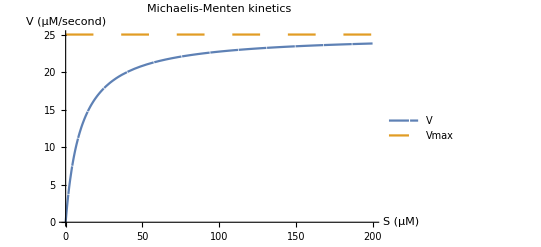

```mathematica
V[S_,Km_,Vmax_]=Vmax (S/(Km+S));
Plot[{V[S,10,25],25},{S,0.,200},AxesLabel->{"S (μM)","V (μM/second)"},PlotStyle->{Dashing[{0.05,0.}],Dashing[{0.05,0.05}]},PlotRange->All,AxesOrigin->{0,0}, PlotLabel->"Michaelis-Menten kinetics", PlotLegends->{"V", "Vmax"}]
```

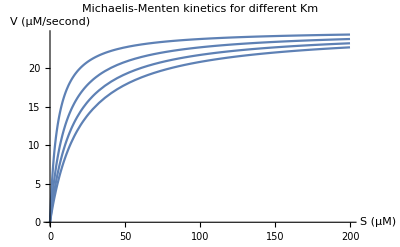

```mathematica
V[S_,Km_,Vmax_]=Vmax (S/(Km+S));
myplot[i_]:=Plot[V[S,i,25],{S,0.,200},AxesLabel->{"S (μM)","V (μM/second)"},PlotRange->All,AxesOrigin->{0,0}]

Show[Table[myplot[i],{i,5,20,5}], 
PlotLabel->"Michaelis-Menten kinetics for different Km", 
PlotLegends->{"Km = 5", "Km = 10", "Km=15", "Km = 20"}]
```

Inhibition kinetics

A number of substrates (so called inhibitors) may cause a reduction in the rate of an enzyme catalyzed reaction. There are three kinds of inhibition: competitive inhibitors bind to the active site on the enzyme; noncompetitive inhibitors bind to a site on the enzyme distinct from the active site; and uncompetitive inhibitors bind to the enzyme only when substrate is also bound to form an enzyme-substrate complex. The equations for the reaction velocity for each of these three cases are:

V_c = (V_max S)/(S+ (1+ I/K_i)K_M) 

V_n = (V_max S)/((1 + I/K_i)( S + K_M))

V_u = (V_max S)/((1 + I/K_i)S + K_M)

where V_c, V_n and  V_u denote the reaction velocity for competitive, noncompetitive and uncompetitive inhibitors, respectively. I is the concentration of inhibitor and K_i denotes the “saturation” constant for inhibitor. A nice introduction about the derivation of the equation for competitive inhibition can be found at the follwing webpage:  http://www.bug-bytes.com/jasonf/msthesis/0A-00.html

## Exercises

Michaelis-Menten Kinetics

Explore the functional behavior of the Michaelis-Menten equation by varying both V_max and K_m and using different substrate concentration (maximum) values. 

a. Briefly describe this behavior. How likely are you able to accurately infer the V_max value from the graph?

```mathematica
ClearAll["Global`*"]

V[S_,Km_,Vmax_]=Vmax (S/(Km+S))

Manipulate[
Plot[
Evaluate[{V[S,Km,Vmax],Vmax}],
{S,0.,Smax},
AxesLabel->{"Substrate concentration (μM)","Reaction rate V (μM/second)"},
ImageSize->Large,
PlotLabel->"Michaelis-Menten kinetics",
PlotStyle->{Dashing[{0.05,0.}],Dashing[{0.05,0.05}]},
PlotRange->All,
PlotLegends->{"V", "Vmax"},
AxesOrigin->{0,0}], 
{{Km, 10}, 0, 100, Appearance->"Labeled"}, 
{{Vmax, 10}, 0, 100, Appearance->"Labeled"}, 
{{Smax, 100}, 50, 1000, Appearance->"Labeled"} ]
```

(S Vmax)/(Km+S)

Explore the functional behavior of the three different kinds of inhibitors (V_c, V_n and V_u) with a constant V_max
( = 12) and K_m (=3), but: 
1. Different K_i values (constant I concentration ( = 5)).

```mathematica
Vcompetitive[S_,Vmax_,Iconc_,Ki_,Km_] =( Vmax * S )/ (S + (1+ Iconc/Ki)*Km)
Vnoncompetitive[S_,Vmax_,Iconc_,Ki_,Km_] = (Vmax*S)/((1+Iconc/Ki)*(S +Km)) 
Vuncompetitive[S_,Vmax_,Iconc_,Ki_,Km_]=(Vmax*S)/((1+Iconc/Ki)S + Km)
```

(S Vmax)/((1+Iconc/Ki) Km+S)

(S Vmax)/((1+Iconc/Ki) (Km+S))

(S Vmax)/(Km+(1+Iconc/Ki) S)

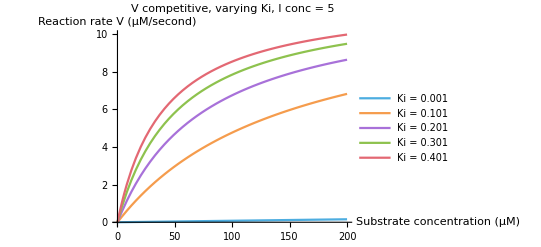

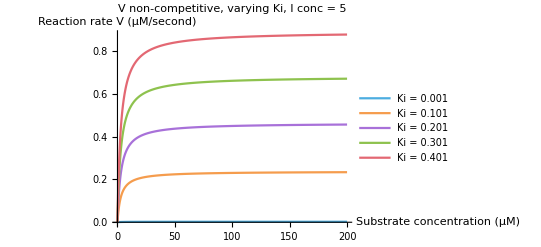

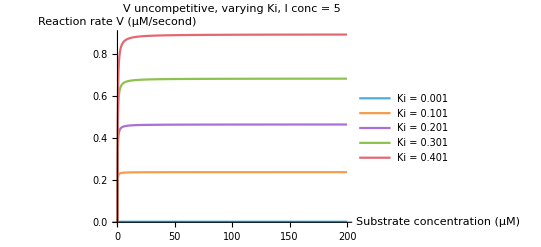

```mathematica
plotje1 = Plot[Evaluate@Table[Vcompetitive[S, 12, 5, Kii, 3], {Kii,0.001,0.5,0.1}], {S,0.,200}, 
PlotLabel->"V competitive, varying Ki, I conc = 5",
AxesLabel->{"Substrate concentration (μM)","Reaction rate V (μM/second)"},
PlotTheme->"PastelColor",
PlotLegends->{"Ki = 0.001", "Ki = 0.101", "Ki = 0.201","Ki = 0.301", "Ki = 0.401"}]

plotje2 = Plot[Evaluate@Table[Vnoncompetitive[S, 12, 5, Kii, 3], {Kii,0.001,0.5,0.1}], {S,0.,200},
PlotLabel->"V non-competitive, varying Ki, I conc = 5",
AxesLabel->{"Substrate concentration (μM)","Reaction rate V (μM/second)"},
PlotTheme->"PastelColor",
PlotLegends->{"Ki = 0.001", "Ki = 0.101", "Ki = 0.201","Ki = 0.301", "Ki = 0.401"}]

plotje3 = Plot[Evaluate@Table[Vuncompetitive[S, 12, 5, Kii, 3], {Kii,0.001,0.5,0.1}], {S,0.,200}, 
PlotLabel->"V uncompetitive, varying Ki, I conc = 5",
AxesLabel->{"Substrate concentration (μM)","Reaction rate V (μM/second)"},
PlotTheme->"PastelColor",
PlotLegends->{"Ki = 0.001", "Ki = 0.101", "Ki = 0.201","Ki = 0.301", "Ki = 0.401"}]
```

2. Different I concentration values (constant K_i ( = 2)).

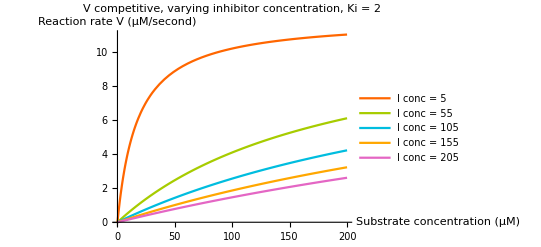

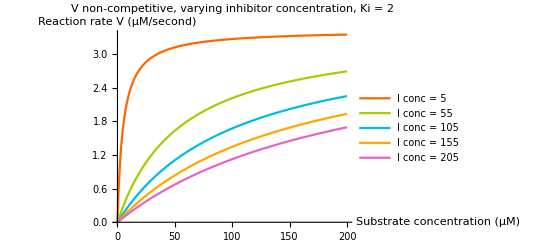

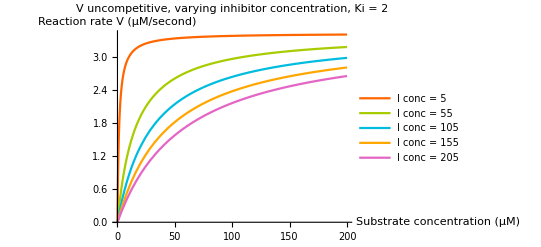

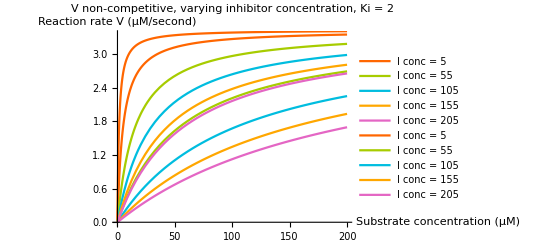

```mathematica
plotje4 = Plot[Evaluate@Table[Vcompetitive[S, 12, 5, 2, ConcII], {ConcII,5,250,50}], {S,0.,200}, 
PlotLabel->"V competitive, varying inhibitor concentration, Ki = 2",
AxesLabel->{"Substrate concentration (μM)","Reaction rate V (μM/second)"},
AxesOrigin->{0,0},
PlotTheme->"NeonColor",
PlotLegends->{"I conc = 5", "I conc = 55", "I conc = 105","I conc = 155", "I conc = 205"}]

plotje5 = Plot[Evaluate@Table[Vnoncompetitive[S, 12, 5, 2, ConcII], {ConcII,5,250,50}], {S,0.,200}, 
PlotLabel->"V non-competitive, varying inhibitor concentration, Ki = 2",
AxesLabel->{"Substrate concentration (μM)","Reaction rate V (μM/second)"}, 
PlotTheme->"NeonColor",
PlotLegends->{"I conc = 5", "I conc = 55", "I conc = 105","I conc = 155", "I conc = 205"}]

plotje6 = Plot[Evaluate@Table[Vuncompetitive[S, 12, 5, 2, ConcII], {ConcII,5,250,50}], {S,0.,200}, 
PlotLabel->"V uncompetitive, varying inhibitor concentration, Ki = 2",
AxesLabel->{"Substrate concentration (μM)","Reaction rate V (μM/second)"}, 
PlotTheme->"NeonColor",
PlotLegends->{"I conc = 5", "I conc = 55", "I conc = 105","I conc = 155", "I conc = 205"}]

Show[plotje5, plotje6]
```

b. Describe the behavior you see and what happened when changing K_i and I values. 

For the competitive inhibitor we see that when the Ki increases, the reaction rate also increases faster. The same goes for the non-competitive and uncompetitive inhibitors. These reach their “plateaus” earlier then the competitive one. The graphs of the non-competitive and uncompetitive inhibitors have the same shape, but the uncompetitive one goes up faster than the non-competitive one.


When we vary the concentration of the inhibitor, we see that the graphs change in the same way as before. For the competitive inhibitor, we see that the substrate concentration keeps increasing, and we don’t really see it reaching the plateau of maximum speed. For the non-competitive one

The reaction rate for I concentration 205 is much lower

Enzymes and inhibitors

The Lineweaver-Burk plot is a plot of 1/V against 1/S, i.e. the inverse of the reaction velocity against the inverse of the substrate concentration. The plot can be used for determining the parameters in enzyme kinetics, e.g. the Michaelis-Menten parameters. Moreover, the plot can distinguish between different types of enzyme inhibition. 
Two other graphical representations that are used more often now are the Hans-Woolf plot and Eadie-Hofstee plot. All approaches have drawbacks, but we will not go into them here (you can read this on the websites if you want to). Let us look a bit closer at the different approaches. 

a. Below there is a generated data list {{S, V},...,...} (measuredData) of measured concentrations and reaction rates. Plot this data and retrieve the Michaelis-Menten parameters from this plot.

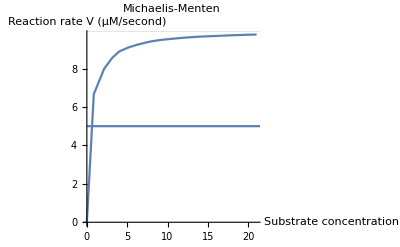

```mathematica
line = ListLinePlot[measuredData];
vmax = Plot[10 ,{x, 0, 25}];

Show[line, vmax, Plot[5, {x, 0 ,25}], 
PlotLabel-> "Michaelis-Menten", 
AxesLabel->{"Substrate concentration (μM)","Reaction rate V (μM/second)"},
ImageSize-> "Large",
PlotLegends->{"V", "Vmax", "Km"}]
```

b. Plot the corresponding Lineweaver-Burke plots and retrieve the Michaelis-Menten parameters.
What can you conclude from this (error wise)?

FittedModel[0.100839+0.0440391 x]

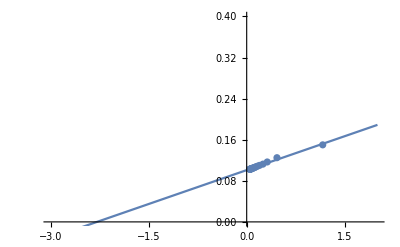

9.91677

0.436726

```mathematica
lineweaverburkData = 1/measuredData⟦2 ;;⟧;
lm = LinearModelFit[lineweaverburkData, x, x]

Show[Plot[lm[x], {x, -3, 2}], ListPlot[lineweaverburkData], PlotRange->{{-3 , 2}, {0,0.4}}]

(* The Lineweaver-Burk (double-reciprocal) plot of 1/v agains 1/s gives intercepts at 1/Vmax and -1/Km *)
Vmax = 1/lm[0]
Km = -((k/.Solve[lm[k] == 0, Reals])^-1)⟦1⟧
```

c. The data (dataI2, dataI8 and dataI8) are from measurements with multiple concentrations of a inhibitor (I = 2, 5, 8) (we made it more convenient for you by importing the data already from an excel file and extracting the part of the list you need. If you want to know more about data importing, visit this link. Find out what kind of inhibitor it is with the Lineweaver-Burk plot. Do the Michaelis-Menten parameters change? Explain why they would or would not.

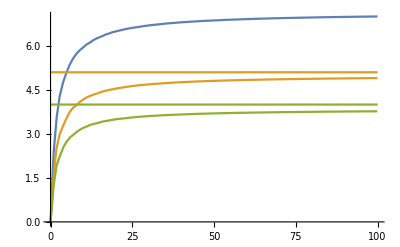

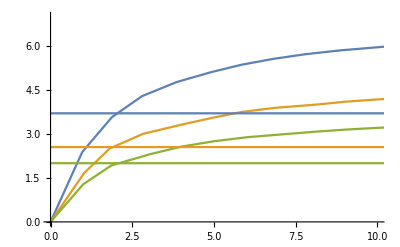

FittedModel[0.140257+0.269287 x]

FittedModel[0.199909+0.398514 x]

FittedModel[0.260184+0.513969 x]

7.12978

5.00229

3.84343

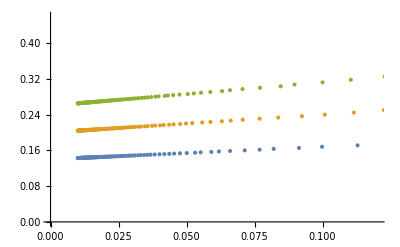

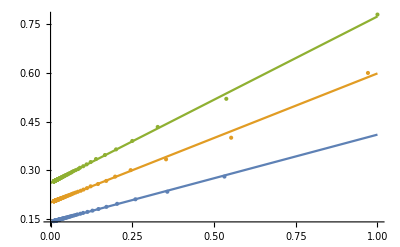

```mathematica
hoi = ListLinePlot[{dataI2, dataI5, dataI8}];
hallo = Plot[{7.2, 5.1, 4.0}, {x, 0, 100}];
Show[hoi, hallo]

hey = ListLinePlot[{dataI2, dataI5, dataI8}];
hi = Plot[{3.7, 2.55, 2.0}, {x, 0, 100}];
Show[hey, hi, PlotRange->{{0 , 10}, {0,7}}]

fit1 =  LinearModelFit[1/dataI2⟦2 ;;⟧, x, x]
fit2 = LinearModelFit[1/dataI5⟦2 ;;⟧, x, x]
fit3 = LinearModelFit[1/dataI8⟦2 ;;⟧, x, x]

Vmaxx = 1/fit1[0]
Vmaxxx = 1/fit2[0]
Vmaxxxx = 1/fit3[0]

talentje = Plot[{fit1[x], fit2[x], fit3[x]}, {x,0,1}];
got = ListPlot[{1/dataI2⟦2 ;;⟧, 1/dataI5⟦2 ;;⟧, 1/dataI8⟦2 ;;⟧}]

Show[talentje, got]
```

Data

```mathematica
measuredData = {{0, 0}, {0.86,6.666},{2.16,8.},{3.18,8.571},{4.02,8.889},{5.12,9.091},{6.19,9.231},{7.15,9.333},{7.98,9.412},{8.94,9.474},{10.,9.524},{11.03,9.565},{11.94,9.6},{12.96,9.63},{13.87,9.655},{15.07,9.678},{16.14,9.697},{17.17,9.714},{17.88,9.729},{19.17,9.743},{19.81,9.756},{21.04,9.767}};
```

```mathematica
dataI2={{0,0},{0.97,2.381},{1.88,3.571},{2.8,4.286},{3.85,4.762},{4.91,5.102},{5.85,5.357},{6.82,5.556},{7.8,5.714},{8.86,5.844},{10.02,5.952},{10.95,6.044},{12.19,6.123},{13.01,6.19},{14.01,6.25},{15.15,6.303},{16.16,6.349},{16.92,6.391},{18.12,6.429},{18.82,6.463},{19.97,6.494},{21.03,6.522},{22.01,6.548},{22.91,6.571},{23.91,6.593},{24.96,6.614},{26.13,6.633},{27.2,6.65},{28.06,6.667},{28.98,6.682},{30.04,6.697},{30.97,6.71},{32.17,6.723},{33.14,6.735},{34.12,6.746},{34.82,6.757},{35.89,6.767},{37.04,6.777},{38.14,6.786},{38.84,6.794},{39.88,6.803},{40.99,6.811},{42.09,6.818},{42.99,6.826},{44.14,6.832},{45.13,6.839},{45.84,6.845},{46.81,6.851},{48.07,6.857},{49.1,6.863},{49.88,6.868},{51.15,6.873},{52.18,6.878},{52.89,6.883},{53.92,6.888},{55.11,6.892},{56.08,6.897},{57.06,6.901},{58.14,6.905},{59.13,6.909},{59.89,6.912},{60.92,6.916},{62.08,6.92},{62.83,6.923},{64.15,6.927},{65.,6.93},{66.05,6.933},{66.86,6.936},{67.91,6.939},{69.01,6.942},{70.12,6.944},{70.96,6.947},{71.83,6.95},{73.08,6.952},{73.97,6.955},{75.01,6.957},{75.96,6.96},{77.08,6.962},{78.,6.964},{79.09,6.967},{80.05,6.968},{80.86,6.971},{82.18,6.973},{82.84,6.975},{83.99,6.977},{84.85,6.979},{85.92,6.98},{86.88,6.983},{87.95,6.984},{88.96,6.986},{90.11,6.988},{91.07,6.989},{92.09,6.991},{93.15,6.993},{94.19,6.994},{94.91,6.996},{96.02,6.997},{97.13,6.998},{98.02,7.},{99.09,7.001},{99.95,7.003}};

dataI5 = {{0,0},{1.03,1.667},{1.81,2.5},{2.83,3.},{4.08,3.333},{5.06,3.572},{5.87,3.75},{6.89,3.889},{8.16,4.},{8.97,4.091},{9.92,4.167},{10.82,4.231},{11.95,4.286},{13.01,4.333},{14.16,4.375},{15.1,4.412},{15.88,4.444},{17.01,4.474},{17.94,4.5},{19.2,4.524},{20.08,4.546},{20.99,4.565},{22.11,4.583},{22.93,4.6},{24.04,4.615},{24.84,4.629},{25.98,4.643},{26.81,4.655},{28.02,4.667},{28.82,4.677},{30.1,4.687},{30.87,4.697},{32.1,4.706},{33.19,4.714},{34.08,4.722},{34.97,4.73},{36.16,4.737},{37.16,4.744},{37.86,4.75},{38.85,4.756},{39.89,4.762},{40.94,4.767},{42.08,4.773},{43.01,4.778},{43.81,4.783},{44.82,4.787},{46.13,4.792},{47.02,4.796},{47.92,4.8},{49.13,4.804},{50.15,4.808},{51.04,4.811},{51.91,4.815},{52.85,4.818},{54.17,4.821},{55.02,4.825},{55.95,4.828},{56.83,4.83},{58.01,4.833},{59.02,4.836},{59.94,4.839},{61.19,4.841},{62.16,4.844},{63.09,4.846},{64.15,4.848},{65.01,4.851},{65.82,4.853},{66.86,4.855},{67.99,4.857},{68.91,4.859},{69.98,4.861},{71.12,4.863},{72.13,4.865},{72.94,4.867},{74.08,4.869},{74.92,4.87},{75.94,4.872},{76.93,4.874},{77.99,4.875},{79.06,4.876},{80.02,4.878},{81.13,4.88},{81.97,4.881},{82.88,4.882},{83.89,4.884},{84.84,4.885},{85.97,4.886},{86.94,4.888},{88.,4.889},{89.09,4.89},{89.92,4.891},{90.99,4.893},{91.82,4.894},{92.91,4.895},{94.07,4.896},{94.94,4.897},{95.92,4.898},{97.,4.899},{97.82,4.9},{99.13,4.901},{99.93,4.902}};

dataI8 = {{0,0},{1.,1.282},{1.86,1.923},{3.05,2.308},{4.,2.564},{4.99,2.747},{6.01,2.885},{7.19,2.992},{8.14,3.077},{9.06,3.147},{10.,3.205},{11.15,3.255},{11.82,3.297},{12.98,3.333},{14.17,3.365},{15.16,3.394},{15.86,3.419},{17.03,3.441},{18.08,3.462},{18.99,3.48},{19.83,3.497},{21.1,3.512},{22.18,3.526},{23.19,3.538},{23.83,3.55},{25.17,3.561},{25.96,3.572},{27.05,3.581},{28.02,3.59},{28.92,3.598},{29.86,3.606},{30.98,3.613},{32.07,3.62},{32.95,3.626},{33.84,3.633},{34.89,3.638},{35.85,3.644},{37.17,3.649},{38.17,3.654},{39.06,3.658},{39.93,3.663},{41.11,3.667},{42.06,3.671},{42.91,3.675},{43.99,3.679},{44.92,3.683},{45.84,3.686},{46.91,3.689},{47.85,3.692},{49.05,3.696},{49.98,3.698},{50.9,3.701},{51.84,3.704},{52.85,3.706},{54.09,3.709},{55.,3.711},{55.87,3.713},{56.82,3.716},{57.91,3.718},{59.04,3.72},{60.09,3.722},{61.18,3.724},{62.18,3.726},{62.95,3.728},{63.96,3.73},{64.93,3.731},{66.11,3.733},{67.,3.735},{68.18,3.736},{68.9,3.738},{70.06,3.739},{70.86,3.741},{72.03,3.742},{73.16,3.744},{73.91,3.745},{75.06,3.746},{76.15,3.747},{77.08,3.749},{77.83,3.75},{79.04,3.751},{79.98,3.752},{81.15,3.753},{82.,3.755},{82.98,3.756},{84.03,3.757},{84.92,3.758},{85.97,3.759},{87.,3.76},{88.17,3.761},{89.2,3.762},{90.02,3.763},{90.87,3.763},{92.18,3.764},{92.81,3.765},{94.2,3.766},{95.12,3.767},{95.83,3.768},{97.04,3.768},{97.91,3.769},{99.1,3.77},{99.87,3.771}};
```

Ionic channels

-Graphics-Figure 1: An Ion channel in closed and open state.
From: http://blog.canacad.ac.jp/wpmu/15matser/2011/09/14/4-1-passive-transport/ 

An ionic channel in a cellular membrane (Fig. 1) can be regarded as special enzymes for mediating ion transportation over a membrane. They can exist in three states : S_1,S_2,S_3. S_1 and S_3 represent closed states on either side of the membrane (no ions can pass through the channel) and S_2 is an open state. On a given cell there are a number of channels and the fractions of channels in states S_1,S_2 and S_3 are designated x, y and z respectively. Transitions between the states follow the schematic diagram:
 
S_1(⇌_k_3)^k_1 S_2→^k_2 S_3 ,

where k_1,k_2 and k_3 are positive rate constants. A differential equation for this system is: 

dx/dt=- k_1 x+k_3 y, dy/dt=k_1 x-(k_2+k_3) y, dz/dt=k_2 y

where 1 ≥ x ≥ 0, 1 ≥ y ≥ 0 , 1 ≥ z ≥ 0 and let us assume k_1=2, k_2=2 and k_3=1

a. Sketch the flow in the x,y plane 
(Hint: use VectorPlot. Hint 2: flow in the (x,y) plane means the direction field (dx/dt,dy/dt)).

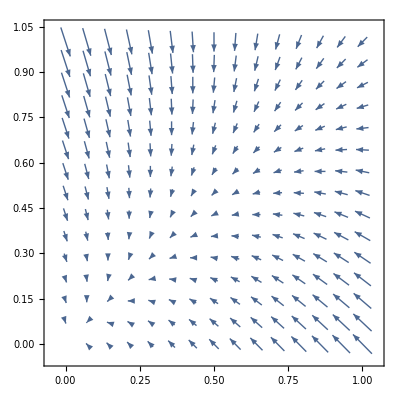

```mathematica
ClearAll["Global`*"]

dx[x_,y_]=-2 x+y;
dy[x_,y_]=2 x-(2+1) y;
dz[x_]=2 y;

VectorPlot[{dx[x,y],dy[x,y]},{x,0,1},{y,0,1}]
```

b. Use NDSolve to solve the equations and give graphs showing x, y ,z as a function of time starting from initial conditions of (1) x = 1, y = 0, z = 0; (2)  x = 0, y = 1, z = 0.  Give an intuitive explanation of why z eventually goes to 1 in both cases.

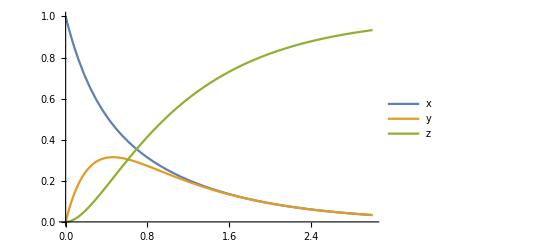

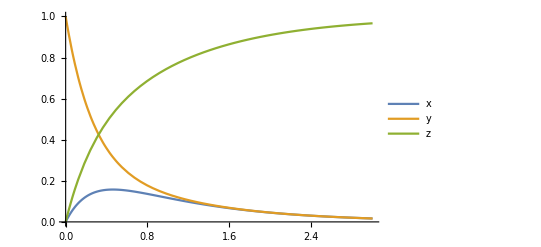

```mathematica
Remove[x, y, z]

solvedFirst[t_]=NDSolve[{x'[t]==-2 x[t]+y[t],y'[t]==2 x[t]-(2+1) y[t],z'[t]==2 y[t],x[0]==1,y[0]==0,z[0]==0},{x[t],y[t],z[t]},{t,0,3}];
solvedSecond[t_]=NDSolve[{x'[t]==-2 x[t]+y[t],y'[t]==2 x[t]-(2+1) y[t],z'[t]==2 y[t],x[0]==0,y[0]==1,z[0]==0},{x[t],y[t],z[t]},{t,0,3}];

Plot[Evaluate[{x[t]/.solvedFirst[t],y[t]/.solvedFirst[t],z[t]/.solvedFirst[t]}],{t,0,3},PlotLegends->{"x","y","z"}]
Plot[Evaluate[{x[t]/.solvedSecond[t],y[t]/.solvedSecond[t],z[t]/.solvedSecond[t]}],{t,0,3},PlotLegends->{"x","y","z"}]
```

c. Assume an initial condition of x = 0, y = 1, z = 0 and assume k_1=0, k_2=2 and k_3=1, solve for x, y, z as a function of time and give an intuitive explanation of why z does not increase to 1 in this case; 
Now assume k_1=0 and k_2,k_3 are arbitrary positive numbers, calculate x and z in terms of k_2 and k_3 (Hint: Using DSolve here).

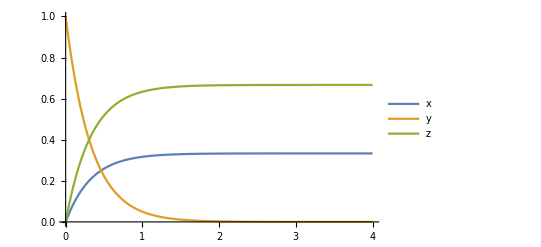

```mathematica
Remove[x,y,z]

solvedC1[t_]=NDSolve[{x'[t]==y[t],y'[t]==-(2+1) y[t],z'[t]==2 y[t],x[0]==0,y[0]==1,z[0]==0},{x[t],y[t],z[t]},{t,0,4}];

Plot[Evaluate[{x[t]/.solvedC1[t],y[t]/.solvedC1[t],z[t]/.solvedC1[t]}],{t,0,4},PlotLegends->{"x","y","z"}]

solvedC2[t_,k2_,k3_]=DSolve[{x'[t,k3]==k3*y[t],y'[t]==-(k2+k3) y[t],z'[t]==k2*y[t],x[0]==0,y[0]==1,z[0]==0},{x[t],y[t],z[t]},{t,0,1},{k2,0,100},{k3,0,100}];
```

```mathematica
ClearAll["Global`*"]
Remove[x,y,z, k1, k2, k3]

DSolve[{x'[t]==k3*y[t],y'[t]==-(k2+k3)* y[t],z'[t]==k2 * y[t], x[0] == 0, y[0] == 1, z[0] == 0},{x[t],y[t],z[t]},t]
```

{{x[t]→-((-1+ⅇ^((-k2-k3) t)) k3)/(k2+k3),y[t]→ⅇ^((-k2-k3) t),z[t]→-((-1+ⅇ^((-k2-k3) t)) k2)/(k2+k3)}}